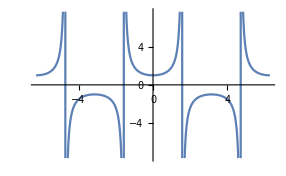

```mathematica
Plot[Sec[x],{x,-2Pi,2Pi}]
```

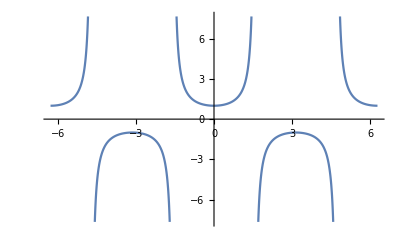

```mathematica
Plot[Sec[x],{x,-2Pi,2Pi},Exclusions->Range[-3Pi/2,3Pi/2,Pi],FrameTicks->{{Automatic,None},{Range[-2Pi,2Pi,Pi],None}}]
```

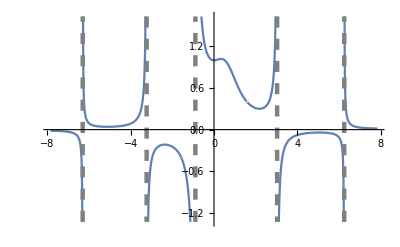

```mathematica
Plot[Sec[x]/(1+x^2 Tan[x]),{x,-5Pi/2,5Pi/2},Exclusions->{Cos[x]==0,1+x^2 Tan[x]==0},ExclusionsStyle->{{Dashing[0.02],Gray,Thickness[0.008]}},FrameTicks->{{Automatic,None},{Range[-2Pi,2Pi,Pi],None}}]
```

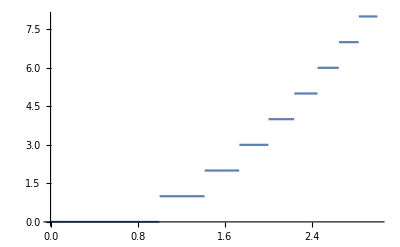

```mathematica
Plot[Floor[x^2],{x,0,3}]
```

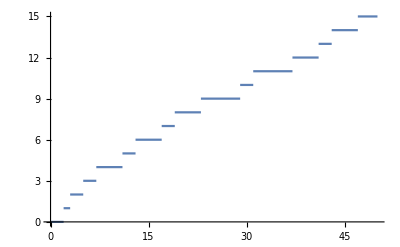

```mathematica
Plot[PrimePi[x],{x,0,50},"SymbolicPiecewiseSubdivision"->True]
```

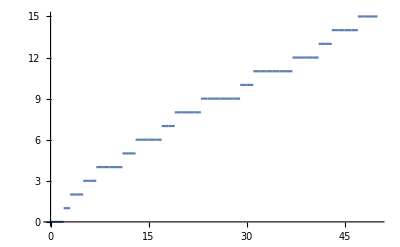

```mathematica
Plot[PrimePi[x],{x,0,50},"SymbolicPiecewiseSubdivision"->True,Exclusions->Range[50]]
```